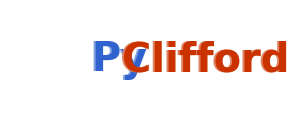

```mathematica
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{Lighter[Blue,0.4],Text[Style["Py",FontSize-> 40,Bold]]},
Translate[{Blue,Text[Style["Py",FontSize-> 40,Bold]]},{0.018,0}],
Translate[{Lighter[Red,0.4],Text[Style["Clifford",FontSize-> 40,Bold]]},{0.95,0}],
Translate[{Red,Text[Style["Clifford",FontSize-> 40,Bold]]},{0.95+0.022,0}],
},ImageSize-> 300,AspectRatio->0.4]
```

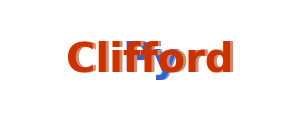

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Translate[{Lighter[col,0.4],#},shift],{col,#}}&@Text[Style[txt,FontFamily->"CMU Sans Serif",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.02,0},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.02,0},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Translate[{Lighter[col,0.4],#},shift],{col,#}}&@Text[Style[txt,FontFamily->"Baloo Bhaijaan",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.02,0},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.02,0},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

-Graphics-

```mathematica
Block[{shadowtext},
shadowtext[txt_,col_,shift_,align_]:={Translate[{Lighter[col,0.4],#},shift],{col,#}}&@Text[Style[txt,FontFamily->"Chalkboard",FontSize-> 40,Bold],{0,0},align];
Graphics[{{Opacity[0],Rectangle[{-1,-1},{1,1}]},{
Translate[shadowtext["Py",Blue,{0.02,0},{1,0}],{0,0}],
Translate[shadowtext["Clifford",Red,{0.02,0},{-1,0}],{0,0}],
}},ImageSize-> 300,AspectRatio->0.4]]
```

-Graphics-